```mathematica
Integrate[ 1/(1+x),{x,0,3}]
```

Log[4]

```mathematica
N[HarmonicNumber[10000]-HarmonicNumber[10000/(E^2)]]
```

1.99968

```mathematica
f[a_]:=Limit[HarmonicNumber[x]-HarmonicNumber[x/a],{x->Infinity}]
```

```mathematica
f[1.4423]
```

{0.366239}

```mathematica
f'[a]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

{Hold[∂_a Limit[HarmonicNumber[x]-HarmonicNumber[x/a],x→∞]]}

```mathematica
Log[1.4423]
```

0.366239

```mathematica
s[n_]:= PolyGamma[n+1]+EulerGamma
```

```mathematica
s[30]-HarmonicNumber[30]
```

0

```mathematica
HarmonicNumber[30]
```

9304682830147/2329089562800

```mathematica
f2[a_]:=Limit[s[x]-s[x/a],{x->Infinity}]
```

```mathematica
f2[10+10I]
```

{-Log[1/20-ⅈ/20]}

```mathematica
Log[10I]
```

(ⅈ π)/2+Log[10]

```mathematica
N[-Log[1/20-ⅈ/20]]
```

2.64916+0.785398 ⅈ

```mathematica
s2[n_]:= PolyGamma[2,n+1]+EulerGamma
```

```mathematica
f3[a_]:=Limit[s2[x]-s2[x/a],{x->Infinity}]
```

```mathematica
Limit[PolyGamma[2,x]-PolyGamma[2,x/81],{x->Infinity}]
```

{0}

```mathematica
Limit[PolyGamma[1,x]-PolyGamma[1,x/81],{x->Infinity}]
```

{0}

```mathematica
Limit[PolyGamma[0,x]-PolyGamma[0,x/81],{x->Infinity}]
```

{Log[81]}

```mathematica
Limit[Gamma'[x]/Gamma[x]-Gamma'[x/81]/Gamma[x/81],{x->Infinity}]
```

{Log[81]}

```mathematica
Limit[Gamma'[x]/Gamma[x]-Gamma'[x/c]/Gamma[x/c],{x->Infinity}]
```

{Limit[PolyGamma[0,x]-PolyGamma[0,x/c],x→∞]}

```mathematica
Integrate[ E^(-t)/t -E^(-z t)/(1-E^(-t)),{t,0,Infinity}]
```

ConditionalExpression[-1/z+PolyGamma[0,1+z],Re[z]>0]

```mathematica
Integrate[-E^(-z t)/(1-E^(-t))+E^(-(z/81) t)/(1-E^(-t)),{t,0,Infinity}]
```

ConditionalExpression[-PolyGamma[0,z/81]+PolyGamma[0,z],Re[z]>0]

```mathematica
Integrate[(E^(-(z/81) t)-E^(-z t))/(1-E^(-t)),{t,0,Infinity}]
```

ConditionalExpression[-PolyGamma[0,z/81]+PolyGamma[0,z],Re[z]>0]

```mathematica
Expand[(E^(-(z/81) t)-E^(-z t))]
```

-ⅇ^(-t z)+ⅇ^(-(t z)/81)

```mathematica
PolyGamma[1/4]
```

PolyGamma[0,1/4]

```mathematica
t[n_, a_] := Mod[n,a]-Mod[n-1,a]
```

```mathematica
t[5,5/2]
```

-3/2

```mathematica
Table[Floor[(a+1)(2/5)],{a,1,10}]
```

{0,1,1,2,2,2,3,3,4,4}

```mathematica
fa[a_] := Floor[(a+1)(2/5)]
```

```mathematica
fa[3]
```

1

```mathematica
fb:={0,-1/4, -1/4,0,-3/3}
```

```mathematica
fb[[2]]
```

-1/4

```mathematica
Table[ fa[n] fb[[Mod[n-1,5]+1]],{n,1,10}]
```

{0,-1/4,-1/4,0,-2,0,-3/4,-3/4,0,-4}

```mathematica
Mod[1,5]
```

1

```mathematica
1-1/6+1/4-3/10+1/6-1/42-1/24+1/9-3/20
```

```mathematica
N[2131/2520]
```

0.845635

```mathematica
N[Log[5/2]]
```

0.916291

```mathematica
1-1/6+1/4-3/10
```

47/60

```mathematica
1+(1/2 -1/2 1)+(1/3-1/2 1)+(1/4)+(1/5-1 1/2)+(1/6)+(1/7 -1/2 1/3)+(1/8-1/2 1/3)+(1/9)+(1/10-1/4) +(1/11)+(1/12 -1/2 1/5)+(1/13-1/2 1/5)+(1/14)+(1/15-1/6)+(1/16)+(1/17 -1/2 1/7)+(1/18-1/2 1/7)+(1/19)+(1/20-1/8)
```

```mathematica
N[68276701/77597520]
```

0.879883

```mathematica
N[62575/72072]
```

0.868229

```mathematica
1+(1/2 -1/2 1)+(1/3-1/2 1)+(1/4)+(1/5-1 1/2)+(1/6)+(1/7 -1/2 1/3)+(1/8-1/2 1/3)+(1/9)+(1/10-1/4) +(1/11)+(1/12 -1/2 1/5)+(1/13-1/2 1/5)+(1/14)+(1/15-1/6)+(1/16)+(1/17 -1/2 1/7)+(1/18-1/2 1/7)+(1/19)+(1/20-1/8)+(1/21)+(1/22 -1/2 1/9)+(1/23-1/2 1/9)+(1/24)+(1/25-1/10)+(1/26)+(1/27 -1/2 1/11)+(1/28-1/2 1/11)+(1/29)+(1/30-1/12)
```

```mathematica
N[2077027228357/2329089562800]
```

0.891776

```mathematica
1+(1/2 -1/2 1)+(1/3-1/2 1)+(1/4)+(1/5-1 1/2)+(1/6)+(1/7 -1/2 1/3)+(1/8-1/2 1/3)+(1/9)+(1/10-1/4) +(1/11)+(1/12 -1/2 1/5)+(1/13-1/2 1/5)+(1/14)+(1/15-1/6)+(1/16)+(1/17 -1/2 1/7)+(1/18-1/2 1/7)+(1/19)+(1/20-1/8)+(1/21)+(1/22 -1/2 1/9)+(1/23-1/2 1/9)+(1/24)+(1/25-1/10)+(1/26)+(1/27 -1/2 1/11)+(1/28-1/2 1/11)+(1/29)+(1/30-1/12)+(1/31)+(1/32 -1/2 1/13)+(1/33-1/2 1/13)+(1/34)+(1/35-1/14)+(1/36)+(1/37 -1/2 1/15)+(1/38-1/2 1/15)+(1/39)+(1/40-1/16)+(1/41)+(1/42 -1/2 1/17)+(1/43-1/2 1/17)+(1/44)+(1/45-1/18)+(1/46)+(1/47 -1/2 1/19)+(1/48-1/2 1/19)+(1/49)+(1/50-1/20)
```

```mathematica
N[2793682265045051088509/3099044504245996706400]
```

0.901466

```mathematica
FF[n_]:=(1/(5n+1))+(1/(5n+2) -1/2 1/1)+(1/(5n+3)-1/2 1/1)+(1/(5n+4))+(1/(5n+5)-1/2)
```

```mathematica
Floor[(5 n+3)*2/5]+2
Floor[(5 n+4)*2/5]+2
```

2+Floor[2/5 (3+5 n)]

2+Floor[2/5 (4+5 n)]

18

18

```mathematica
Floor[(5 n+6)*2/5]+2
```

20

```mathematica
FF2[n_]:=(1/(5n+1))+(1/(5n+2) -1/2 1/(Floor[(5 n)*2/5]+1))+(1/(5n+3)-1/2 1/(Floor[(5 n)*2/5]+1))+(1/(5n+4))+(1/(5n+5)-1/(Floor[(5 n)*2/5]+2))
```

```mathematica
FF2[s]
```

1/(1+5 s)+1/(2+5 s)+1/(3+5 s)+1/(4+5 s)+1/(5+5 s)-1/(1+Floor[2 s])-1/(2+Floor[2 s])

```mathematica
1+(1/2 -1/2 1)+(1/3-1/2 1)+(1/4)+(1/5-1 1/2)
```

47/60

```mathematica
FF2[0]+FF2[1]+FF2[2]+FF2[3]
```

68276701/77597520

```mathematica
FF[0]
```

47/60

```mathematica
1/2 1/(Floor[(5 0+3)*2/5]+2)
```

1/6

```mathematica
N[68276701/77597520]
```

0.879883

```mathematica
N[Sum[ FF2[k],{k,0,13000}]]
```

0.916279

```mathematica
N[Log[5/2]]
```

0.916291

```mathematica
FF3[n_]:=Sum[(1/(5n+a)),{a,1,5}]- (1/(2n+1))-(1/(2n+2))
```

```mathematica
N[Sum[ FF3[k],{k,0,13000}]]
```

0.916279

```mathematica
(5 n)*2/5
```

2 n

```mathematica
FF4[n_]:=Sum[(1/(5n+a)),{a,1,5}]- Sum[(1/(2n+a)),{a,1,2}]
```

```mathematica
N[Sum[ FF4[k],{k,0,13000}]]
```

0.916279

```mathematica
FF5[n_,b_,c_]:=Sum[(1/(b n+a)),{a,1,b}]- Sum[(1/(c n+a)),{a,1,c}]
```

```mathematica
N[Sum[ FF5[k,7,3],{k,0,13000}]]
```

0.847291

```mathematica
N[Log[7/3]]
```

0.847298

```mathematica
S2[ b_, c_]:=N[Sum[ FF5[k,b,c],{k,0,13000}]]
```

```mathematica
S2[1,7]
```

-1.94588

```mathematica
N[Log[1/7]]
```

-1.94591

```mathematica
tt := {-3/2,1,-1/4,-1/4,1}
```

```mathematica
FF[n_] := Sum[ tt[[Mod[k,5]+1]],{k,1,n}]
```

```mathematica
FF[5]
```

0

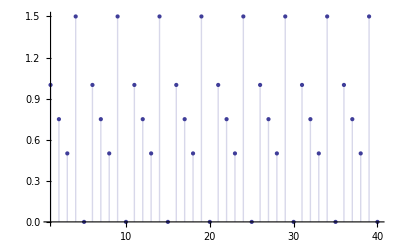

```mathematica
DiscretePlot[ FF[n],{n,1,40}]
```

```mathematica
tt[[Mod[5,5]+1]]
```

-3/2

```mathematica
FFa[n_] := Sum[ tt[[Mod[k,5]+1]]/k,{k,1,n}]
```

```mathematica
FFa[5]
```

89/120

```mathematica
tt2 := {1,0,1/2,1/2,0}
```

```mathematica
FFa[n_] := Sum[ 1/k-tt2[[Mod[k,5]+1]]/(Floor[2(k)/5]+1),{k,1,n}]
```

```mathematica
FFa[5]
```

6/5

```mathematica
Co[k_] :=  1/k-tt2[[Mod[k,5]+1]]/(Floor[2(k-1)/5]+1)
```

```mathematica
Co[10]
```

-3/20

```mathematica
Table[ Co[n],{n,1,50}]
```

{1,0,-1/6,1/4,-3/10,1/6,-1/42,-1/24,1/9,-3/20,1/11,-1/60,-3/130,1/14,-1/10,1/16,-3/238,-1/63,1/19,-3/40,1/21,-1/99,-5/414,1/24,-3/50,1/26,-5/594,-3/308,1/29,-1/20,1/31,-3/416,-7/858,1/34,-3/70,1/36,-7/1110,-2/285,1/39,-3/80,1/41,-2/357,-9/1462,1/44,-1/30,1/46,-9/1786,-5/912,1/49,-3/100}

```mathematica
N[Sum[ Co[k],{k,1,100000}]]
```

0.916283

```mathematica
N[Log[5/2]]
```

0.916291

```mathematica
Co[100004]
```

1/100004

```mathematica
Table[ Co[n],{n,100000,100000+25}]
```

{-3/200000,1/100001,-5000/2000090001,-20001/8000440006,1/100004,-1/66670,1/100006,-20001/8001160042,-10001/4000620024,1/100009,-3/200020,1/100011,-10001/4000980060,-20003/8002040130,1/100014,-3/200030,1/100016,-20003/8002760238,-5001/2000710063,1/100019,-1/66680,1/100021,-5001/2000890099,-20005/8003640414,1/100024,-3/200050}

```mathematica
tt3 := {1,0,0,1,0}
```

```mathematica
Co2[k_] :=  1/k-tt3[[Mod[k,5]+1]]/(Floor[2(k-1)/5]+1)
```

```mathematica
Table[ Co2[n],{n,1,50}]
```

{1,1/2,-2/3,1/4,-3/10,1/6,1/7,-5/24,1/9,-3/20,1/11,1/12,-8/65,1/14,-1/10,1/16,1/17,-11/126,1/19,-3/40,1/21,1/22,-14/207,1/24,-3/50,1/26,1/27,-17/308,1/29,-1/20,1/31,1/32,-20/429,1/34,-3/70,1/36,1/37,-23/570,1/39,-3/80,1/41,1/42,-26/731,1/44,-1/30,1/46,1/47,-29/912,1/49,-3/100}

```mathematica
N[Sum[ Co2[k],{k,1,100000}]]
```

0.916283